```mathematica
PAYOUTSTRUCTURE = {{50,50},{0,100},{100,0},{10,10}};

CalculateFitness[prisonStrategy_,enemyStrategy_,player_]:=
Module[{playerOneStrat,playerTwoStrat,transitionTable,longTerm},
playerOneStrat=prisonStrategy;
playerTwoStrat=enemyStrategy;
transitionTable=CreateTransitionTable[playerOneStrat,playerTwoStrat];
vec=Re[Eigenvectors[Transpose[transitionTable],1][[1]]];
vec=vec/Total[vec];
vec.PAYOUTSTRUCTURE[[All,player]]
];

CreateTransitionTable[stratOne_,stratTwo_]:=
Table[
{stratOne[[i,1]]*stratTwo[[i,1]],stratOne[[i,1]]*stratTwo[[i,2]],stratOne[[i,2]]*stratTwo[[i,1]],stratOne[[i,2]]*stratTwo[[i,2]]}
,{i,1,4}];


MutationDistribution=TruncatedDistribution[{0,1},NormalDistribution[μ,σ]];
Mutation[prisonStrategy_,mutationDeviation_]:=
Module[{chanceOfMutation,newDefect,inputStrategy,temp,newPrisonStrat,newCoop,mutatedStrat},
inputStrategy=prisonStrategy;
Table[
chanceOfMutation=RandomReal[{0,1}];
Which[
chanceOfMutation≤0.1,
newCoop=RandomVariate[MutationDistribution/.{μ->inputStrategy[[i,1]],σ->mutationDeviation}];
newDefect=1-newCoop;
inputStrategy[[i]]={newCoop,newDefect},
chanceOfMutation≥0.1,
inputStrategy[[i]]
]
,{i,1,4}]
];

evaluateGeneration[population_,opposingStrat_,mutability_,player_]:=
Module[{profileOne,profileTwo,resultingPopulation},
resultingPopulation=ConstantArray[0,Length[population]];
Table[
profileOne =RandomChoice[population];
profileTwo =RandomChoice[population];
If[player==1,
Which[
CalculateFitness[profileOne,opposingStrat,player]≥CalculateFitness[profileTwo,opposingStrat,player],
Mutation[profileOne,mutability],
CalculateFitness[profileTwo,opposingStrat,player]≥CalculateFitness[profileOne,opposingStrat,player],
Mutation[profileTwo,mutability]
],
Which[
CalculateFitness[opposingStrat,profileOne,player]≥CalculateFitness[opposingStrat,profileTwo,player],
Mutation[profileOne,mutability],
CalculateFitness[opposingStrat,profileTwo,player]≥CalculateFitness[opposingStrat,profileOne,player],
Mutation[profileTwo,mutability]
]
]
,{i,1,Length[population]}]
];

GenerateStrategeyTable[numStrats_]:=
Table[
Table[
(*N@RandomChoice[IntegerPartitions[1000,{2}]]/1000*)
z = RandomReal[];
{z,1-z}
,{4}]
,numStrats];
```

#### Test Code

```mathematica
a=GenerateStrategeyTable[2];
b=GenerateStrategeyTable[1];
c=GenerateStrategeyTable[1];
CreateTransitionTable[a[[1]],b[[1]]]//MatrixForm;
CalculateFitness[a[[1]],b[[1]],1]≥CalculateFitness[c[[1]],b[[1]],1];
Mutation[a[[1]],.3]//MatrixForm
```

(0.28119 | 0.71881
0.728078 | 0.271922
0.139285 | 0.860715
0.243188 | 0.756812)

#### Actual / Final Code

```mathematica
populationSize=250;
populationOne=GenerateStrategeyTable[populationSize];
populationTwo=GenerateStrategeyTable[populationSize];
mutability=0.3;
snapShotPop=ConstantArray[0,populationSize];
generations=400;
checkSetOne=ConstantArray[0,generations/50];
checkSetTwo=ConstantArray[0,generations/50];
counter=1;
Do[
snapShotPop=RandomChoice[populationTwo];
populationTwo=evaluateGeneration[populationTwo,RandomChoice[populationOne],mutability,2];
populationOne=evaluateGeneration[populationOne,snapShotPop,mutability,1];
If[Mod[i,50]==0,
checkSetOne[[counter]]=Mean[populationOne];
checkSetTwo[[counter]]=Mean[populationTwo];
counter++;
]
,{i,1,generations}
];
```

```mathematica
checkSetOne//MatrixForm
checkSetTwo//MatrixForm
```

((0.573089
0.426911) | (0.218894
0.781106) | (0.126951
0.873049) | (0.204276
0.795724)
(0.855598
0.144402) | (0.126905
0.873095) | (0.0864388
0.913561) | (0.343741
0.656259)
(0.947011
0.0529889) | (0.329035
0.670965) | (0.215303
0.784697) | (0.747656
0.252344)
(0.633355
0.366645) | (0.180418
0.819582) | (0.190284
0.809716) | (0.174294
0.825706)
(0.595099
0.404901) | (0.206254
0.793746) | (0.3946
0.6054) | (0.146774
0.853226)
(0.684533
0.315467) | (0.206454
0.793546) | (0.0848151
0.915185) | (0.0799957
0.920004)
(0.530004
0.469996) | (0.12642
0.87358) | (0.0737249
0.926275) | (0.0396019
0.960398)
(0.307534
0.692466) | (0.304609
0.695391) | (0.124807
0.875193) | (0.0322642
0.967736))

((0.753352
0.246648) | (0.0995931
0.900407) | (0.173401
0.826599) | (0.0453957
0.954604)
(0.940095
0.0599045) | (0.108889
0.891111) | (0.142897
0.857103) | (0.740423
0.259577)
(0.802743
0.197257) | (0.225341
0.774659) | (0.155443
0.844557) | (0.258408
0.741592)
(0.573653
0.426347) | (0.0972923
0.902708) | (0.237977
0.762023) | (0.11431
0.88569)
(0.250194
0.749806) | (0.0537986
0.946201) | (0.104023
0.895977) | (0.0513262
0.948674)
(0.480414
0.519586) | (0.115212
0.884788) | (0.211827
0.788173) | (0.0392655
0.960734)
(0.563011
0.436989) | (0.109491
0.890509) | (0.393797
0.606203) | (0.0744111
0.925589)
(0.50892
0.49108) | (0.0291477
0.970852) | (0.0903253
0.909675) | (0.0340712
0.965929))

```mathematica
a=Table[
CreateTransitionTable[checkSetOne[[i]],checkSetTwo[[i]]]
,{i,1,generations/50}];
a[[8]]//MatrixForm
```

(0.156511 | 0.151024 | 0.35241 | 0.340056
0.00887864 | 0.29573 | 0.0202691 | 0.675122
0.0112732 | 0.113534 | 0.0790521 | 0.796141
0.00109928 | 0.0311649 | 0.0329719 | 0.934764)

```mathematica
b=Table[
vec=Re[Eigenvectors[Transpose[a[[i]]],1][[1]]];
vec/Total[vec]
,{i,1,generations/50}];
b//MatrixForm
```

(0.0214089 | 0.189148 | 0.0566456 | 0.732797
0.400826 | 0.072184 | 0.23414 | 0.29285
0.328532 | 0.308093 | 0.0893223 | 0.274052
0.0338825 | 0.158639 | 0.106456 | 0.701022
0.0112045 | 0.161375 | 0.0451269 | 0.782294
0.00844908 | 0.0880262 | 0.0498273 | 0.853697
0.00872469 | 0.0424202 | 0.10496 | 0.843895
0.00214842 | 0.0466086 | 0.0346634 | 0.916579)

```mathematica
f=Table[
fitOne=CalculateFitness[checkSetOne[[i]],checkSetTwo[[i]],1];
fitTwo=CalculateFitness[checkSetTwo[[i]],checkSetOne[[i]],2];
{fitOne,fitTwo},
{i,1,generations/50}];
f//MatrixForm
Mean[b]
Mean[f]
```

(14.063 | 14.9691
46.3838 | 45.8176
28.0994 | 26.8703
19.35 | 19.9821
12.8959 | 13.1245
13.9422 | 14.2782
19.3712 | 17.7779
12.7396 | 12.8158)

{0.101897,0.133312,0.0901428,0.674648}

{20.8556,20.7044}

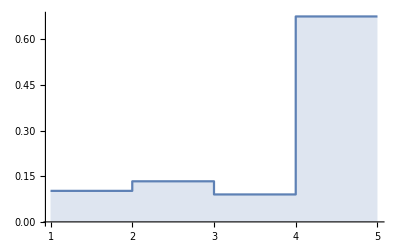

```mathematica
ListStepPlot[Mean[b],Filling->Axis]
```